```mathematica
Needs["Notation`"];
Notation[Δ ⟺ cd]
Notation[𝒿 ⟺ cj]
```

```mathematica
<<sneg`sneg`;
snegfermionoperators[a,b,c];
snegrealconstants[cj,U,U1,t,t22,t23,cd,x];
```

sneg 1.250 Copyright (C) 2016 Rok Zitko

```mathematica
myop = {a[1],a[2],a[3],a[4],a[5],a[6]}
```

{a^,a[2],a[3],a[4],a[5],a[6]}

```mathematica
makebasis[myop]
```

{a_(1⇑)^†,a_(1↓)^†,a_(2⇑)^†,a_(2↓)^†,a_(3⇑)^†,a_(3↓)^†,a_(4⇑)^†,a_(4↓)^†,a_(5⇑)^†,a_(5↓)^†,a_(6⇑)^†,a_(6↓)^†}

```mathematica
vc6= qszbasisvc[myop];
```

```mathematica
basise4p2 = Select[vc6,#[[1]]=={-2,2}&][[1,2]];
```

```mathematica
basise4p1 = Select[vc6,#[[1]]=={-2,1}&][[1,2]];
```

```mathematica
basise40 = Select[vc6,#[[1]]=={-2,0}&][[1,2]];
```

```mathematica
basise4n1 = Select[vc6,#[[1]]=={-2,-1}&][[1,2]];
```

```mathematica
basise4n2= Select[vc6,#[[1]]=={-2,-2}&][[1,2]];
```

```mathematica
hhop = -t22(hop[a[2],a[5]])- t22(hop[a[3],a[6]])-t23(hop[a[2],a[6]]+hop[a[3],a[5]])
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)-t22 (a_(3↓)^†·a_(6↓)^+a_(3⇑)^†·a_(6⇑)^+a_(6↓)^†·a_(3↓)^+a_(6⇑)^†·a_(3⇑)^)

```mathematica
hhd = cd(number[a[3]]+number[a[6]])(* 0.0(number[a[1]]+number[a[2]]+number[a[4]]+number[a[5]])*)
```

Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)

```mathematica
hhj = (U-3cj)(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])
```

(-3 𝒿+U) (-(a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^)-a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^-a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^-a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^-a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^-a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^-a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^-a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^-a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^-a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^-a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)

```mathematica
hhu = U(hubbard[a[1]]+hubbard[a[2]]+hubbard[a[3]]+hubbard[a[4]]+hubbard[a[5]]+hubbard[a[6]])
```

U (-(a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
hhu1 = (*U1(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])+*)(U-2cj)(nc[number[a[1],UP],number[a[2],DO]]+nc[number[a[1],UP],number[a[3],DO]]+nc[number[a[2],UP],number[a[3],DO]]+nc[number[a[1],DO],number[a[2],UP]]+nc[number[a[1],DO],number[a[3],UP]]+nc[number[a[2],DO],number[a[3],UP]]+nc[number[a[4],UP],number[a[5],DO]]+nc[number[a[4],UP],number[a[6],DO]]+nc[number[a[5],UP],number[a[6],DO]]+nc[number[a[4],DO],number[a[5],UP]]+nc[number[a[4],DO],number[a[6],UP]]+nc[number[a[5],DO],number[a[6],UP]])//Simplify
```

(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)

```mathematica
(* U' = U -2J, since Hamiltonian maintains rotation invariance*)
```

```mathematica
(* pair fliping, hhpf*)
```

```mathematica
hhpf1=nc[a[CR,1,UP],a[AN,1,DO],a[CR,2,DO],a[AN,2,UP]]+nc[a[CR,1,UP],a[AN,1,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,2,UP],a[AN,2,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,5,DO],a[AN,5,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,6,DO],a[AN,6,UP]]+nc[a[CR,5,UP],a[AN,5,DO],a[CR,6,DO],a[AN,6,UP]]
```

-(a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^)-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^

```mathematica
hhpf2=conj[hhpf1]
```

-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^

```mathematica
hhpf=-cj (hhpf1+hhpf2)
```

-𝒿 (-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)

```mathematica
(*pair hopping, hhph*)
```

```mathematica
hhph1=nc[a[CR,1,UP],a[AN,2,UP],a[CR,1,DO],a[AN,2,DO]]+nc[a[CR,1,UP],a[AN,3,UP],a[CR,1,DO],a[AN,3,DO]]+nc[a[CR,2,UP],a[AN,3,UP],a[CR,2,DO],a[AN,3,DO]]+nc[a[CR,4,UP],a[AN,5,UP],a[CR,4,DO],a[AN,5,DO]]+nc[a[CR,4,UP],a[AN,6,UP],a[CR,4,DO],a[AN,6,DO]]+nc[a[CR,5,UP],a[AN,6,UP],a[CR,5,DO],a[AN,6,DO]]
```

-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^

```mathematica
hhph2=conj[hhph1]
```

-(a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^

```mathematica
hhph=-cj (hhph1+hhph2)
```

-𝒿 (-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
ham = hhop + hhu + hhj +hhu1+hhd+hhpf+hhph//Simplify
(*ham= hhop + hhu + hhj +hhu1+hhd*)
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)-t22 (a_(3↓)^†·a_(6↓)^+a_(3⇑)^†·a_(6⇑)^+a_(6↓)^†·a_(3↓)^+a_(6⇑)^†·a_(3⇑)^)+Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^+a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^+a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^+a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^+a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^+a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^+a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^+a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^+a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^+a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)+(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)+(3 𝒿-U) (a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^+a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^+a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^+a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^+a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^+a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^+a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^+a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^+a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^+a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)-U (a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
basise4n1;
```

```mathematica
basise40//Dimensions
basise4n1//Dimensions
basise4n2//Dimensions
basise4p2//Dimensions
basise4p1//Dimensions
```

{225}

{120}

{15}

{15}

{120}

```mathematica
mybasis={basise4n1,basise4n2,basise40,basise4p1,basise4p2}//Flatten;
```

```mathematica
td={cd->0.7,cj->U/5,U->6,t23->x t22,t22->0.3}
```

{Δ→0.7,𝒿→U/5,U→6,t23→t22 x,t22→0.3}

```mathematica
{Δ->0.7,𝒿->U/5,U->6,t23->t22 x,t22->0.3}
```

{Δ→0.7,𝒿→U/5,U→6,t23→t22 x,t22→0.3}

```mathematica
mymat=matrixrepresentationop[ham,mybasis]//.td;
```

```mathematica
vals1=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[1]]},{xx,0,2,0.2}];
vals2=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[2]]},{xx,0,2,0.2}];
vals3=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[3]]},{xx,0,2,0.2}];
vals4=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[4]]},{xx,0,2,0.2}];
vals5=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[5]]},{xx,0,2,0.2}];
vals6=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[6]]},{xx,0,2,0.2}];
vals7=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[7]]},{xx,0,2,0.2}];
vals8=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[8]]},{xx,0,2,0.2}];
vals9=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[9]]},{xx,0,2,0.2}];
vals10=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[10]]},{xx,0,2,0.2}];
```

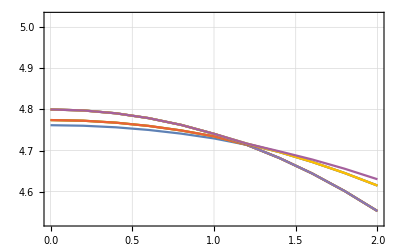

```mathematica
ListLinePlot[{vals1,vals2,vals3,vals4,vals5,vals6,vals7,vals8,vals9,vals10},Frame->True,GridLines->Automatic]
```

```mathematica
(** now we calculate the expection value of the square of spin <|S^2|>, S= s1+s2+s4+s5*)
```

```mathematica
spinpow=spinspin[a[1],a[1]]+spinspin[a[2],a[2]]+spinspin[a[4],a[4]]+spinspin[a[5],a[5]]+2spinspin[a[1],a[2]]+2spinspin[a[1],a[4]]+2spinspin[a[1],a[5]]+2spinspin[a[4],a[5]]+2spinspin[a[2],a[4]]+2spinspin[a[2],a[5]]//Simplify
```

1/4 (3 a_(1↓)^†·a_(1↓)^+3 a_(1⇑)^†·a_(1⇑)^+3 a_(2↓)^†·a_(2↓)^+3 a_(2⇑)^†·a_(2⇑)^+3 a_(4↓)^†·a_(4↓)^+3 a_(4⇑)^†·a_(4⇑)^+3 a_(5↓)^†·a_(5↓)^+3 a_(5⇑)^†·a_(5⇑)^+6 a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^-2 a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+2 a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^-4 a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^-2 a_(1↓)^†·a_(4↓)^†·a_(1↓)^·a_(4↓)^+2 a_(1↓)^†·a_(4⇑)^†·a_(1↓)^·a_(4⇑)^-4 a_(1↓)^†·a_(4⇑)^†·a_(1⇑)^·a_(4↓)^-2 a_(1↓)^†·a_(5↓)^†·a_(1↓)^·a_(5↓)^+2 a_(1↓)^†·a_(5⇑)^†·a_(1↓)^·a_(5⇑)^-4 a_(1↓)^†·a_(5⇑)^†·a_(1⇑)^·a_(5↓)^-4 a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+2 a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^-2 a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-4 a_(1⇑)^†·a_(4↓)^†·a_(1↓)^·a_(4⇑)^+2 a_(1⇑)^†·a_(4↓)^†·a_(1⇑)^·a_(4↓)^-2 a_(1⇑)^†·a_(4⇑)^†·a_(1⇑)^·a_(4⇑)^-4 a_(1⇑)^†·a_(5↓)^†·a_(1↓)^·a_(5⇑)^+2 a_(1⇑)^†·a_(5↓)^†·a_(1⇑)^·a_(5↓)^-2 a_(1⇑)^†·a_(5⇑)^†·a_(1⇑)^·a_(5⇑)^+6 a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-2 a_(2↓)^†·a_(4↓)^†·a_(2↓)^·a_(4↓)^+2 a_(2↓)^†·a_(4⇑)^†·a_(2↓)^·a_(4⇑)^-4 a_(2↓)^†·a_(4⇑)^†·a_(2⇑)^·a_(4↓)^-2 a_(2↓)^†·a_(5↓)^†·a_(2↓)^·a_(5↓)^+2 a_(2↓)^†·a_(5⇑)^†·a_(2↓)^·a_(5⇑)^-4 a_(2↓)^†·a_(5⇑)^†·a_(2⇑)^·a_(5↓)^-4 a_(2⇑)^†·a_(4↓)^†·a_(2↓)^·a_(4⇑)^+2 a_(2⇑)^†·a_(4↓)^†·a_(2⇑)^·a_(4↓)^-2 a_(2⇑)^†·a_(4⇑)^†·a_(2⇑)^·a_(4⇑)^-4 a_(2⇑)^†·a_(5↓)^†·a_(2↓)^·a_(5⇑)^+2 a_(2⇑)^†·a_(5↓)^†·a_(2⇑)^·a_(5↓)^-2 a_(2⇑)^†·a_(5⇑)^†·a_(2⇑)^·a_(5⇑)^+6 a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-2 a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+2 a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^-4 a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-4 a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+2 a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^-2 a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+6 a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
Clear[avs2];
data1={};
Do[
Do[pos1=(Position[Eigensystem[mymat/.x->xx1][[1]],Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]]]//Flatten)[[1]];
e1=Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]];
wf1=Eigensystem[mymat/.x->xx1][[2,pos1]];
fullwf1=Sum[wf1[[i]]mybasis[[i]],{i,1,Dimensions[mybasis][[1]]}];
avs2=(matrixrepresentationop[spinpow,{fullwf1}]//Flatten)[[1]];
AppendTo[data1,{j,xx1,avs2,e1}];
Print[j];
Print[avs2],{xx1,0,2,0.1}],{j,1,10}]
```

1

4.22423×10^-6

1

0.0000947914

1

0.000366753

1

0.000820889

1

0.00145849

1

0.00228132

1

0.00329164

1

0.00449214

1

0.00588589

1

0.00747633

1

0.00926719

1

0.0112624

1

5.92469

1

5.90912

1

5.89167

1

5.87227

1

5.8509

1

5.82753

1

5.80219

1

5.77494

1

5.74586

2

2.

2

1.9999

2

1.99963

2

1.99916

2

1.99851

2

1.99766

2

1.99663

2

1.9954

2

1.99398

2

1.99236

2

1.99054

2

1.98851

2

5.92469

2

5.90912

2

5.89167

2

5.87227

2

5.8509

2

5.82753

2

5.80219

2

5.77494

2

5.74586

3

2.

3

1.9999

3

1.99963

3

1.99916

3

1.99851

3

1.99766

3

1.99663

3

1.9954

3

1.99398

3

1.99236

3

1.99054

3

1.98851

3

5.92469

3

5.90912

3

5.89167

3

5.87227

3

5.8509

3

5.82753

3

5.80219

3

5.77494

3

5.74586

4

2.

4

1.9999

4

1.99963

4

1.99916

4

1.99851

4

1.99766

4

1.99663

4

1.9954

4

1.99398

4

1.99236

4

1.99054

4

1.98851

4

5.92469

4

5.90912

4

5.89167

4

5.87227

4

5.8509

4

5.82753

4

5.80219

4

5.77494

4

5.74586

5

6.

5

5.99958

5

5.9983

5

5.99614

5

5.99305

5

5.98897

5

5.98382

5

5.9775

5

5.96992

5

5.96096

5

5.9505

5

5.93845

5

5.92469

5

5.90912

5

5.89167

5

5.87227

5

5.8509

5

5.82753

5

5.80219

5

5.77494

5

5.74586

6

6.

6

5.99958

6

5.9983

6

5.99614

6

5.99305

6

5.98897

6

5.98382

6

5.9775

6

5.96992

6

5.96096

6

5.9505

6

5.93845

6

0.0134661

6

0.0158825

6

1.98115

6

1.97826

6

1.97514

6

1.97179

6

1.96821

6

1.96438

6

1.96031

7

6.

7

5.99958

7

5.9983

7

5.99614

7

5.99305

7

5.98897

7

5.98382

7

5.9775

7

5.96992

7

5.96096

7

5.9505

7

5.93845

7

1.98627

7

1.98382

7

1.98115

7

1.97826

7

1.97514

7

1.97179

7

1.96821

7

1.96438

7

1.96031

8

6.

8

5.99958

8

5.9983

8

5.99614

8

5.99305

8

5.98897

8

5.98382

8

5.9775

8

5.96992

8

5.96096

8

5.9505

8

5.93845

8

1.98627

8

1.98382

8

1.98115

8

1.97826

8

1.97514

8

1.97179

8

1.96821

8

1.96438

8

1.96031

9

6.

9

5.99958

9

5.9983

9

5.99614

9

5.99305

9

5.98897

9

5.98382

9

5.9775

9

5.96992

9

5.96096

9

5.9505

9

5.93845

9

1.98627

9

1.98382

9

0.0185156

9

0.0213696

9

0.024448

9

0.0277542

9

0.031291

9

0.0350605

9

0.0390639

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

0.744115

10

0.743259

10

0.742363

10

0.741433

10

0.740471

10

0.739482

10

0.73847

10

0.73744

```mathematica
data1//MatrixForm
```

(1 | 0. | 4.22423×10^-6 | 4.7617
1 | 0.1 | 0.0000947914 | 4.76138
1 | 0.2 | 0.000366753 | 4.76042
1 | 0.3 | 0.000820889 | 4.75882
1 | 0.4 | 0.00145849 | 4.75658
1 | 0.5 | 0.00228132 | 4.75369
1 | 0.6 | 0.00329164 | 4.75016
1 | 0.7 | 0.00449214 | 4.74597
1 | 0.8 | 0.00588589 | 4.74114
1 | 0.9 | 0.00747633 | 4.73564
1 | 1. | 0.00926719 | 4.72948
1 | 1.1 | 0.0112624 | 4.72266
1 | 1.2 | 5.92469 | 4.71393
1 | 1.3 | 5.90912 | 4.69856
1 | 1.4 | 5.89167 | 4.68184
1 | 1.5 | 5.87227 | 4.66376
1 | 1.6 | 5.8509 | 4.6443
1 | 1.7 | 5.82753 | 4.62346
1 | 1.8 | 5.80219 | 4.60123
1 | 1.9 | 5.77494 | 4.57761
1 | 2. | 5.74586 | 4.55261
2 | 0. | 2. | 4.77422
2 | 0.1 | 1.9999 | 4.77382
2 | 0.2 | 1.99963 | 4.77263
2 | 0.3 | 1.99916 | 4.77065
2 | 0.4 | 1.99851 | 4.76788
2 | 0.5 | 1.99766 | 4.76431
2 | 0.6 | 1.99663 | 4.75995
2 | 0.7 | 1.9954 | 4.75479
2 | 0.8 | 1.99398 | 4.74884
2 | 0.9 | 1.99236 | 4.74208
2 | 1. | 1.99054 | 4.73453
2 | 1.1 | 1.98851 | 4.72618
2 | 1.2 | 5.92469 | 4.71393
2 | 1.3 | 5.90912 | 4.69856
2 | 1.4 | 5.89167 | 4.68184
2 | 1.5 | 5.87227 | 4.66376
2 | 1.6 | 5.8509 | 4.6443
2 | 1.7 | 5.82753 | 4.62346
2 | 1.8 | 5.80219 | 4.60123
2 | 1.9 | 5.77494 | 4.57761
2 | 2. | 5.74586 | 4.55261
3 | 0. | 2. | 4.77422
3 | 0.1 | 1.9999 | 4.77382
3 | 0.2 | 1.99963 | 4.77263
3 | 0.3 | 1.99916 | 4.77065
3 | 0.4 | 1.99851 | 4.76788
3 | 0.5 | 1.99766 | 4.76431
3 | 0.6 | 1.99663 | 4.75995
3 | 0.7 | 1.9954 | 4.75479
3 | 0.8 | 1.99398 | 4.74884
3 | 0.9 | 1.99236 | 4.74208
3 | 1. | 1.99054 | 4.73453
3 | 1.1 | 1.98851 | 4.72618
3 | 1.2 | 5.92469 | 4.71393
3 | 1.3 | 5.90912 | 4.69856
3 | 1.4 | 5.89167 | 4.68184
3 | 1.5 | 5.87227 | 4.66376
3 | 1.6 | 5.8509 | 4.6443
3 | 1.7 | 5.82753 | 4.62346
3 | 1.8 | 5.80219 | 4.60123
3 | 1.9 | 5.77494 | 4.57761
3 | 2. | 5.74586 | 4.55261
4 | 0. | 2. | 4.77422
4 | 0.1 | 1.9999 | 4.77382
4 | 0.2 | 1.99963 | 4.77263
4 | 0.3 | 1.99916 | 4.77065
4 | 0.4 | 1.99851 | 4.76788
4 | 0.5 | 1.99766 | 4.76431
4 | 0.6 | 1.99663 | 4.75995
4 | 0.7 | 1.9954 | 4.75479
4 | 0.8 | 1.99398 | 4.74884
4 | 0.9 | 1.99236 | 4.74208
4 | 1. | 1.99054 | 4.73453
4 | 1.1 | 1.98851 | 4.72618
4 | 1.2 | 5.92469 | 4.71393
4 | 1.3 | 5.90912 | 4.69856
4 | 1.4 | 5.89167 | 4.68184
4 | 1.5 | 5.87227 | 4.66376
4 | 1.6 | 5.8509 | 4.6443
4 | 1.7 | 5.82753 | 4.62346
4 | 1.8 | 5.80219 | 4.60123
4 | 1.9 | 5.77494 | 4.57761
4 | 2. | 5.74586 | 4.55261
5 | 0. | 6. | 4.8
5 | 0.1 | 5.99958 | 4.79942
5 | 0.2 | 5.9983 | 4.79768
5 | 0.3 | 5.99614 | 4.79476
5 | 0.4 | 5.99305 | 4.79068
5 | 0.5 | 5.98897 | 4.7854
5 | 0.6 | 5.98382 | 4.77893
5 | 0.7 | 5.9775 | 4.77124
5 | 0.8 | 5.96992 | 4.76232
5 | 0.9 | 5.96096 | 4.75215
5 | 1. | 5.9505 | 4.74071
5 | 1.1 | 5.93845 | 4.72798
5 | 1.2 | 5.92469 | 4.71393
5 | 1.3 | 5.90912 | 4.69856
5 | 1.4 | 5.89167 | 4.68184
5 | 1.5 | 5.87227 | 4.66376
5 | 1.6 | 5.8509 | 4.6443
5 | 1.7 | 5.82753 | 4.62346
5 | 1.8 | 5.80219 | 4.60123
5 | 1.9 | 5.77494 | 4.57761
5 | 2. | 5.74586 | 4.55261
6 | 0. | 6. | 4.8
6 | 0.1 | 5.99958 | 4.79942
6 | 0.2 | 5.9983 | 4.79768
6 | 0.3 | 5.99614 | 4.79476
6 | 0.4 | 5.99305 | 4.79068
6 | 0.5 | 5.98897 | 4.7854
6 | 0.6 | 5.98382 | 4.77893
6 | 0.7 | 5.9775 | 4.77124
6 | 0.8 | 5.96992 | 4.76232
6 | 0.9 | 5.96096 | 4.75215
6 | 1. | 5.9505 | 4.74071
6 | 1.1 | 5.93845 | 4.72798
6 | 1.2 | 0.0134661 | 4.71516
6 | 1.3 | 0.0158825 | 4.70697
6 | 1.4 | 1.98115 | 4.6963
6 | 1.5 | 1.97826 | 4.68472
6 | 1.6 | 1.97514 | 4.67234
6 | 1.7 | 1.97179 | 4.65915
6 | 1.8 | 1.96821 | 4.64515
6 | 1.9 | 1.96438 | 4.63034
6 | 2. | 1.96031 | 4.61471
7 | 0. | 6. | 4.8
7 | 0.1 | 5.99958 | 4.79942
7 | 0.2 | 5.9983 | 4.79768
7 | 0.3 | 5.99614 | 4.79476
7 | 0.4 | 5.99305 | 4.79068
7 | 0.5 | 5.98897 | 4.7854
7 | 0.6 | 5.98382 | 4.77893
7 | 0.7 | 5.9775 | 4.77124
7 | 0.8 | 5.96992 | 4.76232
7 | 0.9 | 5.96096 | 4.75215
7 | 1. | 5.9505 | 4.74071
7 | 1.1 | 5.93845 | 4.72798
7 | 1.2 | 1.98627 | 4.71702
7 | 1.3 | 1.98382 | 4.70706
7 | 1.4 | 1.98115 | 4.6963
7 | 1.5 | 1.97826 | 4.68472
7 | 1.6 | 1.97514 | 4.67234
7 | 1.7 | 1.97179 | 4.65915
7 | 1.8 | 1.96821 | 4.64515
7 | 1.9 | 1.96438 | 4.63034
7 | 2. | 1.96031 | 4.61471
8 | 0. | 6. | 4.8
8 | 0.1 | 5.99958 | 4.79942
8 | 0.2 | 5.9983 | 4.79768
8 | 0.3 | 5.99614 | 4.79476
8 | 0.4 | 5.99305 | 4.79068
8 | 0.5 | 5.98897 | 4.7854
8 | 0.6 | 5.98382 | 4.77893
8 | 0.7 | 5.9775 | 4.77124
8 | 0.8 | 5.96992 | 4.76232
8 | 0.9 | 5.96096 | 4.75215
8 | 1. | 5.9505 | 4.74071
8 | 1.1 | 5.93845 | 4.72798
8 | 1.2 | 1.98627 | 4.71702
8 | 1.3 | 1.98382 | 4.70706
8 | 1.4 | 1.98115 | 4.6963
8 | 1.5 | 1.97826 | 4.68472
8 | 1.6 | 1.97514 | 4.67234
8 | 1.7 | 1.97179 | 4.65915
8 | 1.8 | 1.96821 | 4.64515
8 | 1.9 | 1.96438 | 4.63034
8 | 2. | 1.96031 | 4.61471
9 | 0. | 6. | 4.8
9 | 0.1 | 5.99958 | 4.79942
9 | 0.2 | 5.9983 | 4.79768
9 | 0.3 | 5.99614 | 4.79476
9 | 0.4 | 5.99305 | 4.79068
9 | 0.5 | 5.98897 | 4.7854
9 | 0.6 | 5.98382 | 4.77893
9 | 0.7 | 5.9775 | 4.77124
9 | 0.8 | 5.96992 | 4.76232
9 | 0.9 | 5.96096 | 4.75215
9 | 1. | 5.9505 | 4.74071
9 | 1.1 | 5.93845 | 4.72798
9 | 1.2 | 1.98627 | 4.71702
9 | 1.3 | 1.98382 | 4.70706
9 | 1.4 | 0.0185156 | 4.69811
9 | 1.5 | 0.0213696 | 4.68854
9 | 1.6 | 0.024448 | 4.67828
9 | 1.7 | 0.0277542 | 4.66731
9 | 1.8 | 0.031291 | 4.65562
9 | 1.9 | 0.0350605 | 4.64321
9 | 2. | 0.0390639 | 4.63007
10 | 0. | 3.75 | 5.35836
10 | 0.1 | 3.75 | 5.35836
10 | 0.2 | 3.75 | 5.35836
10 | 0.3 | 3.75 | 5.35836
10 | 0.4 | 3.75 | 5.35836
10 | 0.5 | 3.75 | 5.35836
10 | 0.6 | 3.75 | 5.35836
10 | 0.7 | 3.75 | 5.35836
10 | 0.8 | 3.75 | 5.35836
10 | 0.9 | 3.75 | 5.35836
10 | 1. | 3.75 | 5.35836
10 | 1.1 | 3.75 | 5.35836
10 | 1.2 | 3.75 | 5.35836
10 | 1.3 | 0.744115 | 5.35248
10 | 1.4 | 0.743259 | 5.33755
10 | 1.5 | 0.742363 | 5.32154
10 | 1.6 | 0.741433 | 5.30446
10 | 1.7 | 0.740471 | 5.28631
10 | 1.8 | 0.739482 | 5.26711
10 | 1.9 | 0.73847 | 5.24686
10 | 2. | 0.73744 | 5.22556)

```mathematica
(****now we calculate J1 and J2 as well as β = -J2/J1, J1= (1/2)(E2-E1), J2 = E0/3+E2/6-E1/2****)
```

```mathematica
Dimensions[data1]
```

{210,4}

```mathematica
tmp01=data1[[1;;12,1;;4]];
tmp02 = data1[[118;;119,1;;4]];
tmp03 = data1[[183;;189,1;;4]];
tmp04=Flatten[{tmp01,tmp02,tmp03},1];
e0data=Table[{tmp04[[i,2]],tmp04[[i,4]],tmp04[[i,3]]},{i,Dimensions[tmp04][[1]]}];
```

```mathematica
tmp01=data1[[22;;33,1;;4]];
tmp02 = data1[[139;;147, 1;;4]];
tmp03=Flatten[{tmp01,tmp02},1];
e1data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp01=data1[[85;;105,1;;4]];
tmp03=Flatten[{tmp01},1];
e2data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp03=data1[[190;;210,1;;4]];

e4data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
e0data//MatrixForm
e1data//MatrixForm
e2data//MatrixForm
```

(0. | 4.7617 | 4.22423×10^-6
0.1 | 4.76138 | 0.0000947914
0.2 | 4.76042 | 0.000366753
0.3 | 4.75882 | 0.000820889
0.4 | 4.75658 | 0.00145849
0.5 | 4.75369 | 0.00228132
0.6 | 4.75016 | 0.00329164
0.7 | 4.74597 | 0.00449214
0.8 | 4.74114 | 0.00588589
0.9 | 4.73564 | 0.00747633
1. | 4.72948 | 0.00926719
1.1 | 4.72266 | 0.0112624
1.2 | 4.71516 | 0.0134661
1.3 | 4.70697 | 0.0158825
1.4 | 4.69811 | 0.0185156
1.5 | 4.68854 | 0.0213696
1.6 | 4.67828 | 0.024448
1.7 | 4.66731 | 0.0277542
1.8 | 4.65562 | 0.031291
1.9 | 4.64321 | 0.0350605
2. | 4.63007 | 0.0390639)

(0. | 4.77422 | 2.
0.1 | 4.77382 | 1.9999
0.2 | 4.77263 | 1.99963
0.3 | 4.77065 | 1.99916
0.4 | 4.76788 | 1.99851
0.5 | 4.76431 | 1.99766
0.6 | 4.75995 | 1.99663
0.7 | 4.75479 | 1.9954
0.8 | 4.74884 | 1.99398
0.9 | 4.74208 | 1.99236
1. | 4.73453 | 1.99054
1.1 | 4.72618 | 1.98851
1.2 | 4.71702 | 1.98627
1.3 | 4.70706 | 1.98382
1.4 | 4.6963 | 1.98115
1.5 | 4.68472 | 1.97826
1.6 | 4.67234 | 1.97514
1.7 | 4.65915 | 1.97179
1.8 | 4.64515 | 1.96821
1.9 | 4.63034 | 1.96438
2. | 4.61471 | 1.96031)

(0. | 4.8 | 6.
0.1 | 4.79942 | 5.99958
0.2 | 4.79768 | 5.9983
0.3 | 4.79476 | 5.99614
0.4 | 4.79068 | 5.99305
0.5 | 4.7854 | 5.98897
0.6 | 4.77893 | 5.98382
0.7 | 4.77124 | 5.9775
0.8 | 4.76232 | 5.96992
0.9 | 4.75215 | 5.96096
1. | 4.74071 | 5.9505
1.1 | 4.72798 | 5.93845
1.2 | 4.71393 | 5.92469
1.3 | 4.69856 | 5.90912
1.4 | 4.68184 | 5.89167
1.5 | 4.66376 | 5.87227
1.6 | 4.6443 | 5.8509
1.7 | 4.62346 | 5.82753
1.8 | 4.60123 | 5.80219
1.9 | 4.57761 | 5.77494
2. | 4.55261 | 5.74586)

```mathematica
|
```

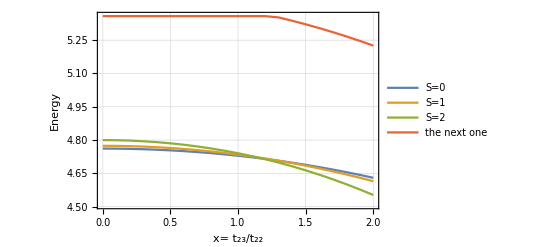

```mathematica
ListLinePlot[{e0data[[1;;21,1;;2]],e1data[[1;;21,1;;2]],e2data[[1;;21,1;;2]],e4data[[1;;21,1;;2]]},PlotLegends->{"S=0","S=1","S=2","the next one"},Frame->True,GridLines->Automatic,AxesLabel->{"x= t_23/t_22","Energy"}]
```

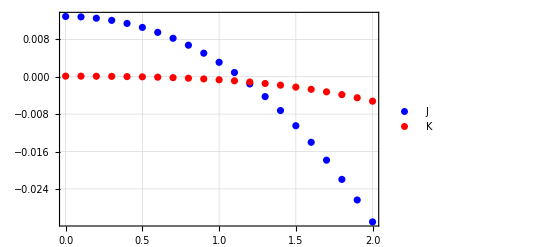

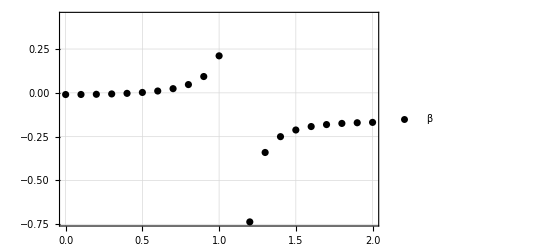

```mathematica
jj1=Table[{e2data[[i,1]],(e2data[[i,2]]-e1data[[i,2]])/2},{i,1,Dimensions[e1data][[1]]}];
jj2=Table[{e2data[[i,1]],e0data[[i,2]]/3.0+e2data[[i,2]]/6.0-e1data[[i,2]]/2.0},{i,1,Dimensions[e1data][[1]]}];
beta=Table[{e2data[[i,1]],-jj2[[i,2]]/jj1[[i,2]]},{i,1,Dimensions[jj1][[1]]}];
ListPlot[{jj1,jj2},PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"J","K"},{Left,Center}],PlotStyle->{Blue,Red}]
ListPlot[beta,PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"β"},{Left,Center}],PlotStyle->Black]
```